```mathematica
L = 5
```

5

```mathematica
T = 240
```

240

```mathematica
U = 1
```

1

```mathematica
(* CP is 1/2 of base LP pool liquidity in millions of dollars *)
```

```mathematica
CP = 10
```

10

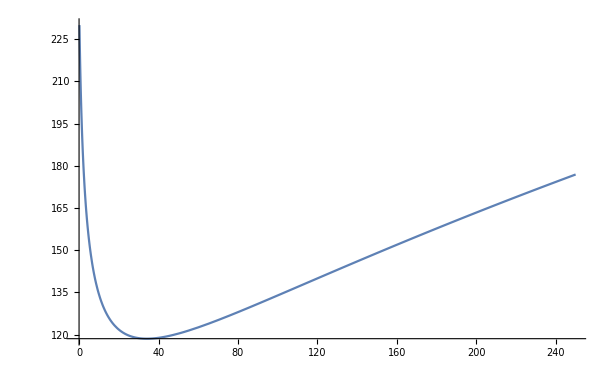

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]) + U)*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

```mathematica
FindMinimum[CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x]
```

{118.564,{x→34.1436}}

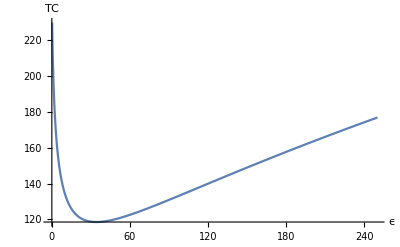

```mathematica
Show[%27,AxesLabel->{HoldForm[ϵ],HoldForm[TC]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/Users/personal/Desktop/tc_10m.svg",%30,"SVG"]
```

/Users/personal/Desktop/tc_10m.svg

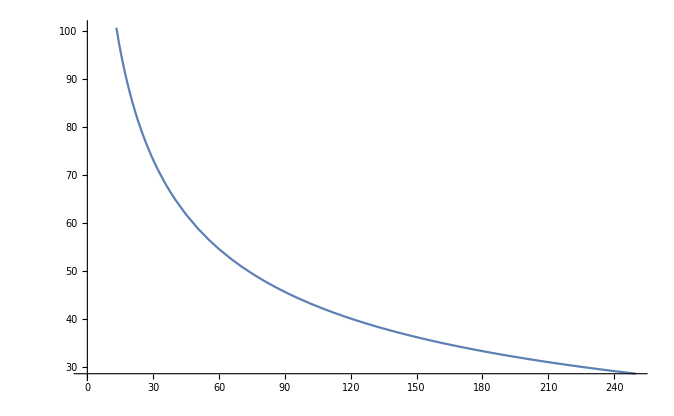

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]))*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x))*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

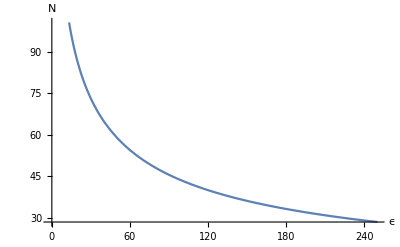

```mathematica
Show[%36,AxesLabel->{HoldForm[ϵ],HoldForm[N]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
CP*(T/(L*34.14359353944894))*(Sqrt[1+34.14359353944894]-1)
```

69.282

```mathematica
(* Caps on OI can be made s.t. N break-even in [35] is not possible *)
```

```mathematica
(* What about taking advantage of TWAP as lagging metric? Bid/ask spread needs to be added *)
```

```mathematica
(* If using 1h TWAP, and know accumulator value right now, want to maximize probability bid/ask we offer is NOT profitable vs TWAP 1 hour into the future when value catches up to current spot price *)
```

```mathematica
(* Looking at B = P0 * e^{1/Δ * (X_t + F^{-1}_X(1-α))}, where X = Σ X_i *)
```

```mathematica
(* Examine for 1h TWAP on ETH/DAI. Distribution ... *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandle = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044,0.0015427669619594313]
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
edistWethUsdc90dFiltered1HourCandle = StableDistribution[1,1.597679462042982,-0.0971291600175433,-0.00015725436055898914,0.007900125269736371]
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandle , 0.999]
```

0.184654

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled1Hour = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044*6,0.0015427669619594313*(6)^(1/1.4646547203677354)]
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.00524308]

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.999]
```

0.195974

```mathematica
(* Ok so close :) *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.999]]
```

1.0332

```mathematica
(* And if simply do 99% of time ... *)
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]
```

0.0424508

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]]
```

1.0071

```mathematica
(* Nice. Another 0.7% on top of the effect of the jump in price on twap at 99% confidence *)
```

```mathematica
(* And for 95% confidence? ... *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.95]]
```

1.00271

```mathematica
(* imagine a 5% jump in 10 min, what does that translate to in the twap? ... *)
```

```mathematica
x5pc10min = Log[1.05]
```

0.0487902

```mathematica
Exp[x5pc10min/6.0]
```

1.00816

```mathematica
(* Translates to 0.8% jump in twap. So buy/long price would be 1.5% greater than current TWAP price *)
```

```mathematica
(* and a 10% jump in 10 min ... *)
```

```mathematica
x10pc10min = Log[1.10]
```

0.0953102

```mathematica
Exp[x10pc10min/6.0]
```

1.01601

```mathematica
(* Translates to 1.6% jump in twap immediately. So buy/long price would be 2.3% greater than current twap price *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.9975]]
```

1.01776